```mathematica
Integrate[-9/2 (BesselJ[1, x]/x)^2, {x, 0, Infinity}]
```

-6/π

```mathematica
g[x_] := 1 -9/2(SphericalBesselJ[1,x]/x)^2
```

```mathematica
Limit[g[x], x->0]
```

1/2

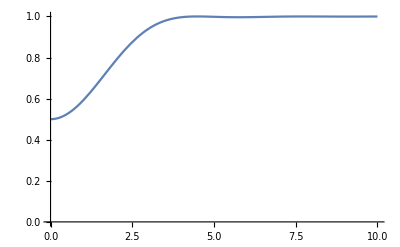

```mathematica
Plot[g[x], {x, 0, 10}, PlotRange->{0,1}]
```